# Real Analysis, Lecture #23

```mathematica
F[x_]:=NIntegrate[Sin[t^3],{t,-1,Cos[x]}]
```

```mathematica
f[x_]:=-Sin[x]*Sin[(Cos[x])^3]
```

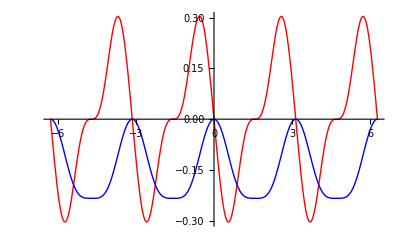

```mathematica
Plot[{f[x],F[x]},{x,-2π,2π},PlotStyle->{{Thick,Red},{Thick,Blue}}]
```

## Properties of Integrals

## The Fundamental Theorem of Calculus (FTC)

```mathematica
∫E^(-x^2)ⅆx
```

1/2 √π Erf[x]

```mathematica
Kinney[x_]:=NIntegrate[Sin[t^3+E^(t)]*Cos[t],{t,0,x}]
```

```mathematica
Plot[{Sin[x^3+E^(x)]*Cos[x],Kinney[x]},{x,0,4},PlotStyle->{{Thick,Blue},{Thick,Red}}]
```

```mathematica
D[(1/2)x*Sqrt[1-x^2]+(1/2)ArcSin[x],x]//Simplify
```

√(1-x^2)

## Application: Water Flow

```mathematica
f[t_]:=Piecewise[{{t+3, -3≤t<-2}, {1, -2≤t<4}, {-(t-4)+1, 4≤t≤7}}];F[t_]:=Piecewise[{{t^2/2+3t+7, -3≤t<-2}, {t+5, -2≤t≤4}, {-3+5t-t^2/2, 4<t≤7}}];plot=Plot[{f[t],F[t]},{t,-3,7},PlotStyle->{{Thick,Blue},{Thick,Red}},AspectRatio->Automatic,AxesLabel->{"time (min)"," "},PlotRange->{-3,10}];tank=Graphics[{Thick,Black,Line[{{{-4,6},{-4,5},{-5,5},{-5,-5},{3,-5},{3,-6}},{{4,-6},{4,-5},{5,-5},{5,5},{-3,5},{-3,6}}}]},Axes->True];Manipulate[Grid[{{Show[tank,Graphics[{Red,Rectangle[{-5,-5},{5,-5+F[t]}]}],Graphics[{Blue,Rectangle[{-3.5-If[-3≤t≤5,f[t],0]/10 ,-5+F[t]},{-3.5+If[-3≤t≤5,f[t],0]/10 , 7}]}],Graphics[{Blue,Rectangle[{3.5-If[-3≤t≤5,0,f[t]]/10 ,-7},{3.5+If[-3≤t≤5,0,f[t]]/10 , -5}]}]],Show[plot,ListPlot[{{t,f[t]},{t,F[t]}},PlotStyle->{Black,PointSize[.05]}]]}}],{t,-3,7}]
```

```mathematica
f[t_]:=3Cos[t];F[t_]:=3Sin[t]+5;plot=Plot[{f[t],F[t]},{t,-3,7},PlotStyle->{{Thick,Blue},{Thick,Red}},AspectRatio->Automatic,AxesLabel->{"time (min)"," "},PlotRange->{-3,10}];tank=Graphics[{Thick,Black,Line[{{{-4,6},{-4,5},{-5,5},{-5,-5},{3,-5},{3,-6}},{{4,-6},{4,-5},{5,-5},{5,5},{-3,5},{-3,6}}}]},Axes->True];Manipulate[Grid[{{Show[tank,Graphics[{Red,Rectangle[{-5,-5},{5,-5+F[t]}]}],Graphics[{Blue,Rectangle[{-3.5-If[f[t]≥0,f[t],0]/10 ,-5+F[t]},{-3.5+If[f[t]≥0,f[t],0]/10 , 7}]}],Graphics[{Blue,Rectangle[{3.5-If[f[t]≥0,0,f[t]]/10 ,-7},{3.5+If[f[t]≥0,0,f[t]]/10 , -5}]}]],Show[plot,ListPlot[{{t,f[t]},{t,F[t]}},PlotStyle->{Black,PointSize[.05]}]]}}],{t,-3,7}]
```

```mathematica
f[t_]:=3Cos[t]+2Cos[3t];F[t_]:=3Sin[t]+2Sin[3t]/3+5;plot=Plot[{f[t],F[t]},{t,-3,7},PlotStyle->{{Thick,Blue},{Thick,Red}},AspectRatio->Automatic,AxesLabel->{"time (min)"," "},PlotRange->{-6,10}];tank=Graphics[{Thick,Black,Line[{{{-4,6},{-4,5},{-5,5},{-5,-5},{3,-5},{3,-6}},{{4,-6},{4,-5},{5,-5},{5,5},{-3,5},{-3,6}}}]},Axes->True];Manipulate[Grid[{{Show[tank,Graphics[{Red,Rectangle[{-5,-5},{5,-5+F[t]}]}],Graphics[{Blue,Rectangle[{-3.5-If[f[t]≥0,f[t],0]/10 ,-5+F[t]},{-3.5+If[f[t]≥0,f[t],0]/10 , 7}]}],Graphics[{Blue,Rectangle[{3.5-If[f[t]≥0,0,f[t]]/10 ,-7},{3.5+If[f[t]≥0,0,f[t]]/10 , -5}]}]],Show[plot,ListPlot[{{t,f[t]},{t,F[t]}},PlotStyle->{Black,PointSize[.05]}]]}}],{t,-3,7}]
```

## Differential Equations and Antiderivatives

### Example: Solve the IVP dy/dx=x^3-4x, y(0)=2

```mathematica
Show[VectorPlot[{1,x^3-4x},{x,-3,3},{y,-3,3},Axes->True,VectorScale->{.03,.03,None},VectorPoints->30,AxesLabel->{"x","y"}],Plot[{1/4 x^4-2x^2+2,1/4 x^4-2x^2+1},{x,-3,3},PlotStyle->{{Thick,Red},{Thick,Magenta}}]]
```

### Example: Solve the IVP dy/dx=sin(x), y(0)=0

```mathematica
Show[VectorPlot[{1,Sin[x]},{x,-2Pi,2Pi},{y,-3,3},Axes->True,VectorScale->{.03,.03,None},VectorPoints->30],Plot[{-Cos[x]+1,-Cos[x]},{x,-2Pi,2Pi},PlotStyle->{{Thick,Red},{Thick,Magenta}}]]
```

### A hard example: Solve the IVP dy/dx=√(1-x^2), y(0)=0

```mathematica
∫√(1-x^2)ⅆx
```

```mathematica
Show[VectorPlot[{1,√(1-x^2)},{x,-1,1},{y,-3,3},Axes->True,VectorScale->{.03,.03,None},VectorPoints->30],Plot[1/2 (x √(1-x^2)+ArcSin[x]),{x,-1,1},PlotStyle->{{Thick,Red},{Thick,Magenta}}]]
```

```mathematica
Manipulate[Grid[{{Plot[f[x],{x,0,b},PlotRange->{{0,1},{0,1}},PlotStyle->{Thick,Magenta},Filling->Axis,AspectRatio->1]},{Plot[F[x],{x,0,b},PlotRange->{{0,1},{0,1}},PlotStyle->{Thick,Blue},AspectRatio->1]}}],{b,.0001,1}]
```

### An even harder example: Solve the IVP dy/dx=sin(x^2), y(0)=2

```mathematica
∫Sin[x^2]ⅆx
```

√(π/2) FresnelS[√(2/π) x]

```mathematica
∫Cos[x^2]ⅆx
```

√(π/2) FresnelC[√(2/π) x]

```mathematica
F[x_]:=2+∫_0^x Sin[t^2]ⅆt
```

```mathematica
Show[VectorPlot[{1,Sin[x^2]},{x,-5,5},{y,-3,3},Axes->True,VectorScale->{.03,.03,None},VectorPoints->50],Plot[F[x],{x,-5,5},PlotStyle->{Thick,Red}]]
```

## Substitution

## Integration-by-Parts

## Average Value of a Riemann Integrable Function

### The average value of a Riemann integrable function f over an interval [a,b] is V=f̄=1/(b-a)∫_a^b f

### Geometric Interpretation

```mathematica
f[x_]:=2x^2-x^3;Manipulate[Plot[{f[x],1/(b-a)∫_a^b f[t]ⅆt},{x,a,b},PlotStyle->{{Thick,Red},{Thick,Blue}},Filling->Axis,PlotRange->{{0,3},{-3,3}}],{a,0,1},{b,1,3}]
```

### Another Approach

```mathematica
RandomReal[]
```

0.132624

```mathematica
f[1.3*RandomReal[]]
```

1.12121

```mathematica
Mean[Table[f[1.3*RandomReal[]],{i,1,10000}]]
```

0.577172

```mathematica
1/1.3*∫_0^1.3 f[x]ⅆx
```

0.577417

```mathematica
f[x_]:=2x^2-x^3;Manipulate[Mean[Table[f[(b-a)*RandomReal[]+a],{i,1,1000}]],{a,0,1},{b,1,3}]
```

```mathematica
Plot[1/b∫_0^b f[t]ⅆt,{b,1,3},PlotStyle->Thick]
```

### Generalization to Higher-Dimensional Integrals

```mathematica
f[x_,y_]:=x^2*y+3x*y+y^3
```

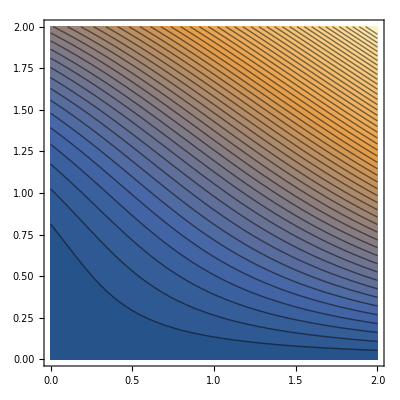

```mathematica
ContourPlot[f[x,y],{x,0,2},{y,0,2},Contours->50]
```

```mathematica
∫_0^2 ∫_0^2 f[x,y]ⅆxⅆy//N
```

25.3333

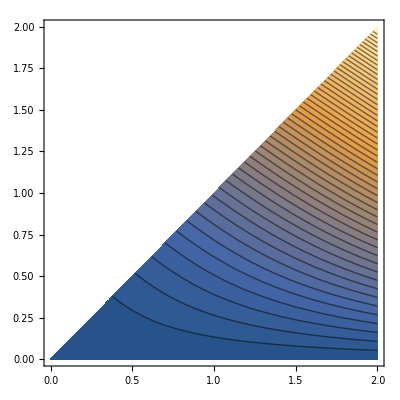

```mathematica
ContourPlot[f[x,y],{x,0,2},{y,0,2},Contours->50,RegionFunction->Function[{x,y},0≤y≤x]]
```

```mathematica
∫_0^2 ∫_0^x f[x,y]ⅆyⅆx
```

54/5

## The Mean Value Theorem for Integrals

## Infinite Series and Partial Sums

```mathematica
∑_(k=1)^∞ 1/(k^2+7k+12)
```

1/4

```mathematica
∑_(k=1)^∞ 1/k^2
```

π^2/6

```mathematica
∑_(k=1)^∞ 1/k^20
```

(174611 π^20)/1531329465290625

```mathematica
∑_(k=1)^∞ 1/k^3
```

Zeta[3]